```mathematica
(*g=9.81;
rho=1000;
L=0.1;
W=0.29;
H=0.05;
V=L*W*H;
A=L*W;
massORIGINAL=680*V;

buoyancy=;
d=massORIGINAL/(rho*g*A)*)
```

```mathematica
Clear["Global`*"]
pitchEXP=Import[NotebookDirectory[]<>"/SPHERIC_TestCase12/Rotation.dat"][[1;;]];
pitchEXP[[1]]
pitchEXP=pitchEXP[[2;;]];
motionsEXP=Import[NotebookDirectory[]<>"/SPHERIC_TestCase12/Motions.dat"][[1;;]];
motionsEXP[[1]]
heaveEXP={#1,#2}&@@@motionsEXP[[2;;,{1,2}]];
surgeEXP=motionsEXP[[2;;,{3,4}]];

name="~/BEM/Hadzic2005_water300/result.json";
floatname="floatingbody";
Quiet[heave=(data=floatname<>"_COM"/.Import[name])[[;;,3]]-(0.4-0.03+0.05/2);];
Quiet[surge=(data=floatname<>"_COM"/.Import[name])[[;;,1]]+(4.-2.11);];
Quiet[pitch=(data=floatname<>"_pitch"/.Import[name]);];
Quiet[force=(data=floatname<>"_force"/.Import[name]);];
Quiet[area=(data=floatname<>"_area"/.Import[name]);];
Quiet[Vx=(data=floatname<>"_velocity"/.Import[name])[[;;,1]];];
Quiet[Vy=(data=floatname<>"_velocity"/.Import[name])[[;;,2]];];
Quiet[Vz=(data=floatname<>"_velocity"/.Import[name])[[;;,3]];];
Quiet[time="time"/.Import[name];];
(*Kramer20210d03=Import[NotebookDirectory[]<>"Kramer2021_0d3.csv"];*)
H0=30/1000;
```

{Time,(s),Roll,(degrees)}

{Time,(s),Heave,(m),Time,(s),Sway,(m)}

```mathematica
Column@Table[Import[name][[i]][[1]],{i,1,Length[Import[name]]}]
```

floatingbody_accel
floatingbody_velocity
floatingbody_COM
floatingbody_force
floatingbody_torque
floatingbody_EK
floatingbody_EP
floatingbody_area
floatingbody_pitch
floatingbody_roll
floatingbody_yaw
time
water_E
water_EK
water_EP
water_volume

```mathematica
ListPlot[Transpose[{time,force}]]
```

-Graphics-

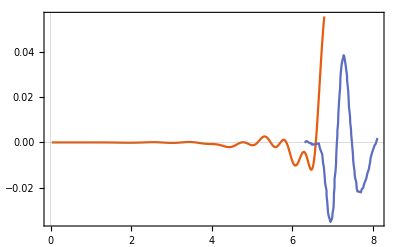

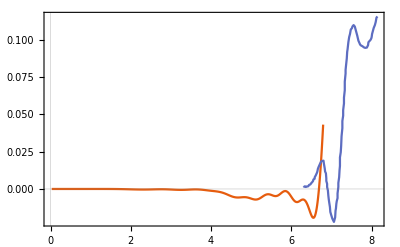

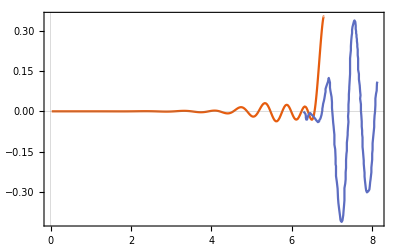

```mathematica
ListPlot[{Transpose[{time,heave}],{#1,#2}&@@@heaveEXP},PlotLabel->"Heave",PlotRange->All,Joined->True,PlotTheme->"Scientific"]
ListPlot[{Transpose[{time,surge}],{#1,#2}&@@@surgeEXP},PlotLabel->"Surge",PlotRange->All,Joined->True,PlotTheme->"Scientific"]
ListPlot[{Transpose[{time,pitch}],{#1,#2/180*Pi}&@@@pitchEXP},PlotLabel->"Pitch",PlotRange->All,Joined->True,PlotTheme->"Scientific"]
```

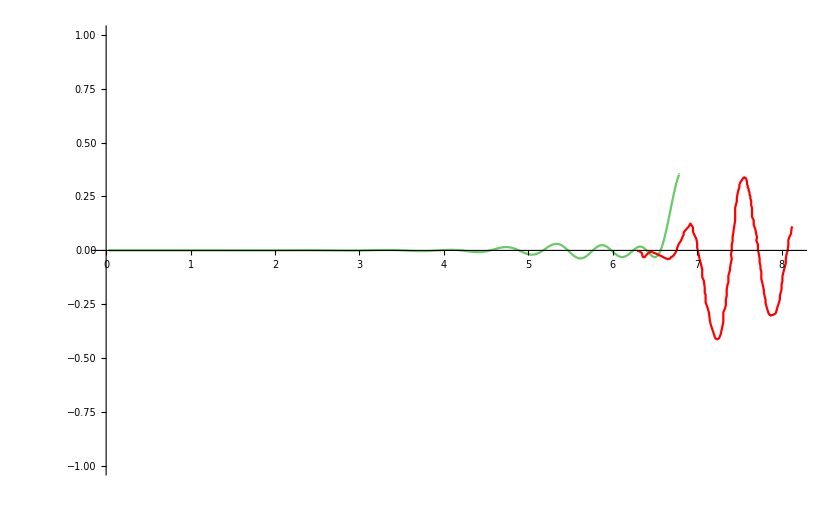

```mathematica
ListPlot[
{Transpose[{time,pitch}],{#1,#2/180*Pi}&@@@pitchEXP},
PlotStyle->{{Darker[Green],Opacity[0.6]},{Red},{Dashed,Blue,Opacity[0.6]},{Thick}},
Joined->{True,True,True},
PlotRange->{Automatic,{-1,1}}
(*PlotRange->{{0,2.25},{-1.,1.}},*)
(*PlotTheme->"Scientific",
Frame->True,
Mesh->All,
GridLines->{Table[i,{i,0.,4.,0.2}],Table[i,{i,-1.,1.,0.5}]},
Frame->True,
FrameLabel->{Style["t/T",FontSize->20,Italic],Style["H/H_0",FontSize->20,Italic]},
FrameStyle->Directive[FontSize->20,Black,Thickness[0.002]],GridLines->{Table[i,{i,0.,4.,0.2}],Table[i,{i,-1.,1.,0.5}]},GridLinesStyle->Directive[Gray,Dotted],
PlotTheme->"Scientific",
ImageSize->500,
PlotLegends->Placed[LineLegend[{"Measured Data","Simulated Data"},LegendMarkerSize->20,LabelStyle->20],{0.75,0.15}]*)
]
```